Render Pixel

<|index→8078,radius→0,ld→{0.0765485,0.0313763,0.00766909},vp_p→{533.157,514.105,-9.9476×10^-13},vp_wo→{-0.186764,-0.961868,0.199824},vp_bsdf→<|eta→1,ns→{0.,0.,1.},ng→{0.,0.,1.},ss→{1.,0.,0.},ts→{0.,-1.,0.},bxdfs0→<|type→LambertianReflection,R→{0.886932,0.696855,0.666832}|>|>,vp_beta→{1,1,1},phi→{},m→0,n→0,tau→{0,0,0}|>

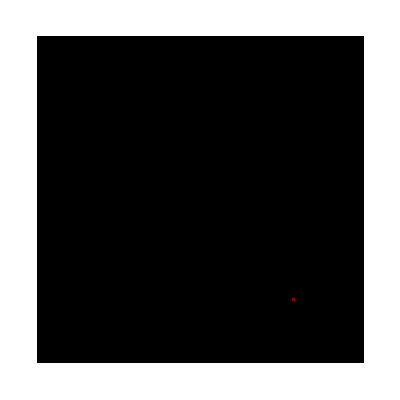

```mathematica
SetDirectory[FileNameJoin@{ParentDirectory[NotebookDirectory[]],"Shared"}];
Needs["gPlots3DEx`"];
Needs["gPlotsEx`"]; 
Needs["gBRDF`"];
Needs["gUtils`"];
Needs["pbrtPath`"];
Needs["pbrtPathLog`"];
SetDirectory[NotebookDirectory[]];

ClearAll[sppmPixelArray,sppmRenderPixelEntry,getSppmPixelOffset,getSppmPixel,
	sppmIntegratorRender,sppmGenVisPoints,sppmGenVisPointsBounce,updateSppmPixel,
	sppmTracePhotonsBounce,sppmComputePixelRadiance,sppmIntegratorRenderIteration,
	sppmImgTable,sppmImgColorMul];

sppmPixelArray=<||>;
sppmImgColorMul=1;

sppmRenderPixelEntry[pixel_,scene_,nIteration_,maxDepth_]:=Module[
{tileMin,tileMax},
tileMin={pixel[[1]],pixel[[2]]};
tileMax={pixel[[1]],pixel[[2]]};

sppmIntegratorRender[tileMin,tileMax,scene,nIteration,maxDepth]
];

(*SPPMIntegrator::Render*)
sppmIntegratorRender[tileMin_,tileMax_,scene_,nIteration_,maxDepth_]:=Module[
{nPixels,resx,resy,iter,i,tmp},
resx=scene["resx"];
resy=scene["resy"];

(*init SPPM pixels*)
nPixels=resx*resy;
For[i=0,i<nPixels,i++,
sppmPixelArray[ToString@i]=<|"index"->i,"radius"->0,"ld"->{0,0,0},
"vp_p"->{0,0,0},"vp_wo"->{0,0,0},"vp_bsdf"-><||>,"vp_beta"->{1,1,1},
"phi"->{},"m"->0,"n"->0,"tau"->{0,0,0}|>
];

(*init image table*)
sppmImgTable=Table[1,resx,resy];
For[i=1,i≤resx,i++,
For[j=1,j≤resy,j++,
 imgTable[[i]][[j]]=RGBColor[0,0,0];
]
];

(*sppmIntegratorRenderIteration*)
For[iter=0,iter<nIteration,iter++,
tmp=sppmIntegratorRenderIteration[iter,tileMin,tileMax,scene,nIteration,maxDepth];
];

tmp
];

(*sppmIntegratorRenderIteration*)
sppmIntegratorRenderIteration[iter_,tileMin_,tileMax_,scene_,nIteration_,maxDepth_]:=Module[
{i,j,pixel},

(*Part_1: sppmGenVisPoints*)
For[i=tileMin[[1]],i≤tileMax[[1]],i++,
For[j=tileMin[[2]],j<=tileMax[[2]],j++,
pixel={i,j};
sppmGenVisPoints[pixel,scene,maxDepth];
];
];

(*Part_2:sppmTracePhotons*)
sppmTracePhotons[pixel,scene,maxDepth];

(*Part_3:sppmUpdatePixelValues*)

(*Part_4:sppmComputePixelRadiance*)
If[iter+1==nIteration,sppmComputePixelRadiance[pixel,scene,nIteration]];

1
];

(*Part_1: sppmGenVisPoints*)
sppmGenVisPoints[pixel_,scene_,maxDepth_]:=Module[
{camRayo,camRayd,beta,visPts,sppmPixel},
sppmPixel=getSppmPixel[pixel,scene];

camRayo=gAssocData[scene,"eyePt"];
camRayd=pbrtRayDifferential[pixel,scene];

(*Part_1:sppmGenVisPointsBounce*)
beta={1,1,1};
visPts=sppmGenVisPointsBounce[pixel,{camRayo,camRayd},beta,scene,0];

visPts
];

(*Part_1:sppmGenVisPointsBounce*)
sppmGenVisPointsBounce[pixel_,ray_,beta_,scene_,bounceIndex_]:=Module[
{rayo,rayd,l,ld,isect1,isectWithBsdf,wo,tmpL,endLabel},
rayo=ray[[1]];
rayd=ray[[2]];
l={0,0,0};
ld={0,0,0};

isect1=pbrtSceneIntersect[ray,scene];
If[ToString@isect1=="NaN",Goto[endLabel]];

(*Compute BSDF at SPPM camera ray intersection*)
isectWithBsdf=pbrtComputeScatteringFunctions[isect1];
If[ToString@isectWithBsdf=="NaN",Goto[endLabel]];

(*Accumulate direct illumination at SPPM camera ray intersection*)
wo=-rayd;
tmpL=If[bounceIndex>0,{0,0,0},pbrtSurfaceInteractionLe[isect1,wo]];
ld+=beta*tmpL;
tmpL=pbrtUniformSampleOneLight[isectWithBsdf,scene];
ld+=beta*tmpL;

updateSppmPixel[pixel,scene,"ld",ld];
updateSppmPixel[pixel,scene,"vp_p",isectWithBsdf["p"]];
updateSppmPixel[pixel,scene,"vp_wo",wo];
updateSppmPixel[pixel,scene,"vp_bsdf",isectWithBsdf["bsdf"]];
updateSppmPixel[pixel,scene,"vp_beta",beta];

Label[endLabel];

];

(*Part_2:sppmTracePhotons*)
sppmTracePhotons[pixel_,scene_,maxDepth_]:=Module[
{uLight0,uLight1,light,lightPdf,
lightLe,le,photonRay,lightNormal,pdfPos,pdfDir,
beta,endLabel},
uLight0=pbrtGet2D[];
uLight1=pbrtGet2D[];

light=scene["lights"][[1]];
lightPdf=1;

lightLe=pbrtLightSampleLe[light,uLight0,uLight1];
le=lightLe["l"];
photonRay=lightLe["photonRay"];
lightNormal=lightLe["lightNormal"];
pdfPos=lightLe["pdfPos"];
pdfDir=lightLe["pdfDir"];

If[pdfPos==0||pdfDir==0||pbrtIsBlack[le],Goto[endLabel]];
beta=(Abs@Dot[lightNormal,photonRay[[2]]]*le)/(lightPdf * pdfPos * pdfDir);
If[pbrtIsBlack[beta],Goto[endLabel]];

(*Part_2:sppmTracePhotonsBounce*)
sppmTracePhotonsBounce[photonRay,beta,scene,0];

Label[endLabel];
lightLe
];

(*Part_4:sppmComputePixelRadiance*)
sppmComputePixelRadiance[pixel_,scene_,nIteration_]:=Module[
{sppmPixel,iter,ld,l},
sppmPixel=getSppmPixel[pixel,scene];

Assert[nIteration==1];
iter=0;
ld=sppmPixel["ld"];
l=ld/(iter+1);

sppmImgTable[[pixel[[2]]+1]][[pixel[[1]]+1]]=
	RGBColor[l[[1]],l[[2]],l[[3]]] * sppmImgColorMul;
];

(*Part_2:sppmTracePhotonsBounce*)
sppmTracePhotonsBounce[photonRay_,beta_,scene_,bounceIndex_]:=Module[
{},

1
];

getSppmPixelOffset[pixel_,scene_]:=Module[
{pixelOffset},

pixelOffset=pixel[[1]] + pixel[[2]]*scene["resx"];
pixelOffset
];

getSppmPixel[pixel_,scene_]:=Module[
{pixelOffset,sppmPixel},

pixelOffset=getSppmPixelOffset[pixel,scene];
sppmPixel=sppmPixelArray[ToString@pixelOffset];

sppmPixel
];

updateSppmPixel[pixel_,scene_,key_,value_]:=Module[
{pixelOffset,sppmPixel},

pixelOffset=getSppmPixelOffset[pixel,scene];
sppmPixelArray[ToString@pixelOffset][key]=value
];


ClearAll[scene,l1,debugPixel,sppmPixel];
sppmImgColorMul=10;
scene=pbrtLoadScene["cornell-tiny.scene"];
debugPixel={78,80};
(*debugPixel={51,12};*)
gPrint["Render Pixel"];
l1=sppmRenderPixelEntry[debugPixel,scene,1,1];
sppmPixel=getSppmPixel[debugPixel,scene];
sppmPixel
ArrayPlot[sppmImgTable]
```